```mathematica
Clear["Global`*"];
```

# Apportionment Algorithms

Every ten years, after the decennial Census, the U.S. reallocates the 435 members of Congress based on updated state populations. This has major implications for both legislation and presidential elections, since a state's electoral votes are determined the size of its delegation. Is there a better way?

## Loading the Data

While Mathematica has population conveniently built in to state entities through the Wolfram Data Repository, let's be extra careful and use the same decennial Census figures the government has used for apportionment, as well as the official number of representatives per state allotted every tens years to compare to alternate methods. This data is conveniently organized on Census.gov and gathered in `getPopulationApportionment.nb`

```mathematica
Clear["Global`*"];
SetDirectory@NotebookDirectory[];
SetOptions[Notebooks["apportionment_local.nb"][[1]],AutoGeneratedPackage->Automatic]
```

```mathematica
statesByAbbreviation = CloudGet["https://www.wolframcloud.com/objects/1a4bfb31-d5d4-49e3-9e04-4cf80e1fae1b"];
(* statesByAbbreviation = Import["./data/state_population_reps_evs.wl"]; *)
```

Let's check that this loaded correctly with all the data we need

```mathematica
stateAbbrs = Keys@statesByAbbreviation;
```

## How it works now: The Huntington-Hill method

Since the 1940 Census, the United States has used the Huntington-Hill algorithm, known as the "method of equal proportions," to divvy up the 435 House seats. This begins by allotting one electoral vote to each state, leaving 385 left. The 50 states are then allotted these remaining seats one-by-one according to which one has the highest priority as determined by a simple equation: its population divided by the square root of its current seats times one extra seat (the Geometric Mean):

P/(√(n (1+n)))

"https://en.wikipedia.org/wiki/United_States_congressional_apportionment#The_method_of_equal_proportions""https://en.wikipedia.org/wiki/United_States_congressional_apportionment#The_method_of_equal_proportions"

Let's make this equation a function for a given state, getting the 2010 decennial Census data from the data we loaded and feeding it the current number of allocated seats

```mathematica
priorityHuntingtonHill[stateAbbr_, stateEVs_] := 
	1.0 * statesByAbbreviation[stateAbbr]["population_decennial"]["2010"] / 
	Sqrt[stateEVs * (stateEVs + 1)]
```

The allocation function will assign electoral votes according to the above formula one at a time. We're also going to explicitly pass the priority function in case we want to try a different one later, which we definitely will, and parameterize all aspects of the allocation algorithm:

To save time, we' re also going to store the priorities until we update the number of seats in a state rather than run 50 square roots 385 times.

total_ is the total number of seats to allocate, defaulting to 435

min_ is the default number of seats that every state begins with, defaulting to 1

priorityFunc_ is the means of determining a state's priority, defaulting to the Huntington-Hill function defined above

```mathematica
(* We need a list of state abbreviations without DC since it is not factored into allocation -- "Taxation Without Representation!" *)
stateAbbrs50 = Select[stateAbbrs, # != "DC"&];

AllocateOne[evs_, priorities_, priorityFunc_:priorityHuntingtonHill] := (
	topPriority = First[Keys[Reverse[Sort[priorities]]]];
	updatedPriorities = priorities;
	updatedEVs = evs;
	updatedEVs[topPriority] += 1;
	updatedPriorities[topPriority] = priorityFunc[topPriority, updatedEVs[topPriority]];
	{ updatedEVs, updatedPriorities }
);

calculateAllocations[total_:435, min_:1, priorityFunc_:priorityHuntingtonHill]:= (
	stateEVs = AssociationThread[stateAbbrs50, ConstantArray[min, 50]];
	statePriorities = AssociationThread[stateAbbrs50, priorityFunc[#, 1]& /@ stateAbbrs50];
	While[Total@stateEVs < total, { stateEVs, statePriorities } = AllocateOne[stateEVs, statePriorities, priorityFunc]];
	KeySort@stateEVs
);
```

Here goes nothing:

```mathematica
results = calculateAllocations[]; 
{results["AL"], results["KY"], results["CA"]}
Total[results]
```

And let's see how it performs with a huge House of Representations

```mathematica
bigHouse = calculateAllocations[2000];
```

## Visualizing the outputs

Let's write a function to compare our calculated allocations to the official ones

```mathematica
calculatedReps = bigHouse;
```

```mathematica
houseOfRepresentatives2010 = AssociationThread[
	stateAbbrs50,
	statesByAbbreviation[#]["representatives"]["2010"]& /@ stateAbbrs50
];
```

```mathematica
statePopulations = AssociationThread[
	stateAbbrs50,
	statesByAbbreviation[#]["population_decennial"]["2010"]& /@ stateAbbrs50
];
```

```mathematica
peoplePerRepresentative[allocation_] := (
	perRep = AssociationThread[
		Keys@allocation,
		Round[statePopulationsWithUS[#] / allocation[#] * 1.0]& /@ Keys@allocation
	]
)
```

```mathematica
(* base values *)
headers = Style[#, TextAlignment -> Center, FontSize->12]& /@ { "State", "House", "Calculated", "Delta", "Per Rep\nHouse", "Per Rep\nCalculated" };
stateLabels = Keys@calculatedReps;
diffs = calculatedReps - houseOfRepresentatives2010;
```

```mathematica
(* colors *)
green = RGBColor["#47C045"];
purple = RGBColor["#E165FA"];
orange = RGBColor["#FF703B"];
maxReps = Max[{Max[calculatedReps], Max[houseOfRepresentatives2010]}];
maxDiff = Max[Abs /@ diffs];
colorScaleReps = Function[d, Blend[Transpose[{{-maxReps / 4, maxReps}, { White, orange }}], d]];
colorScaleDiff = Function[d, Blend[Transpose[{{-maxDiff, 0, maxDiff}, { green, White, purple }}], d]];
colorFunctionReps = Function[v, colorScaleReps[v]];
colorFunctionDiff = Function[v, colorScaleDiff[v]];
```

```mathematica
Grid
```

```mathematica
(* colorFunctionReps = Function[v, If[v == houseOfRepresentatives2010["US"], Yellow, colorScaleReps[v]]]; *)
```

```mathematica
ratioHouse = peoplePerRepresentative[houseOfRepresentatives2010];
ratioCalculated = peoplePerRepresentative[calculatedReps];
```

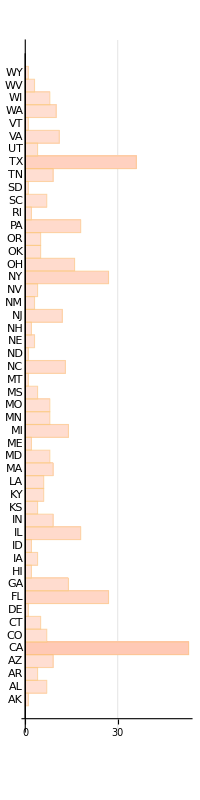
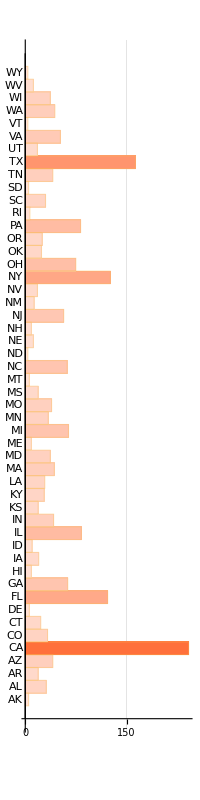

```mathematica
(* bar charts *)
bcHouse = BarChart[houseOfRepresentatives2010[#]& /@ stateLabels,
	ChartLabels->stateLabels,
	BarOrigin->Left, GridLines->Automatic, ImageSize->{200, 800}, AspectRatio->4,
	PlotRangePadding -> { 10, 0 }, PlotRange->{ Automatic, Max[calculatedReps] },
	ColorFunctionScaling -> False,
	ColorFunction->colorFunctionReps
];

bcCalculated = BarChart[calculatedReps[#]& /@ stateLabels,
	ChartLabels->stateLabels,
	BarOrigin->Left, GridLines->Automatic, ImageSize->{200, 800}, AspectRatio->4,
	PlotRangePadding -> { 10, 0 }, PlotRange->{ Automatic, Max[calculatedReps] },
	ColorFunctionScaling -> False,
	ColorFunction->colorFunctionReps
];

Row[{bcHouse, bcCalculated}, BaselinePosition->Top]
```

BarChart::sclfn: The scaling function {Reverse,Identity} cannot be used to scale coordinates.

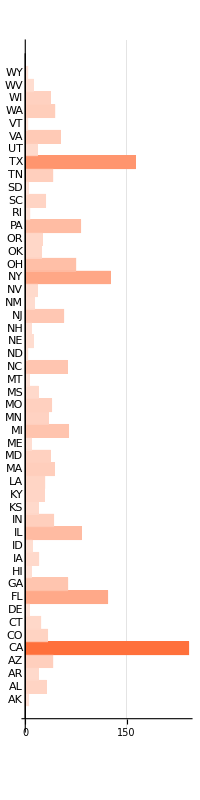

```mathematica
(* data *)
headers = Style[#, TextAlignment -> Center, FontSize->12]& /@ { "State", "House", "Calculated", "Delta", "Per Rep\nHouse", "Per Rep\nCalculated" };
stateLabelsWithUS = Append[Keys@calculatedReps, "US"];
houseOfRepresentatives2010WithUS = Append[houseOfRepresentatives2010, "US" -> Total@houseOfRepresentatives2010];
calculatedRepsWithUS = Append[calculatedReps, "US" -> Total@calculatedReps];
diffsWithUS = calculatedRepsWithUS - houseOfRepresentatives2010WithUS;
statePopulationsWithUS = Append[statePopulations, "US" -> Total@statePopulations];
ratioHouseWithUS = peoplePerRepresentative[houseOfRepresentatives2010WithUS];
ratioCalculatedWithUS = peoplePerRepresentative[calculatedRepsWithUS];
```

```mathematica
ChartLabels->labels, GridLines->Automatic, ImageSize->{800, Automatic}, AspectRatio->1/4,
		PlotRangePadding -> { -1, 0 }, PlotRange->{ Automatic, Max[sorted] * 1.1 }, ChartStyle->Purple,
		ColorFunctionScaling -> False,
		ColorFunction->colorFunction,
		PlotLabel-> Column[{
			Style[ToString@total <> " Seats", FontSize->20],
			Style["Target: " <> ToString@NumberForm[ideal, DigitBlock -> 3] <> " people per representative", FontSize->14],
			Style["Standard Deviation: " <> ToString[sdPrint], FontSize->14],
			Style["Coefficient of Variation: " <> ToString@cov, FontSize->14]
		}, Alignment->Center],
		BarSpacing->None
```

```mathematica
total = Total@allocation
ratioWithUS = Append[ratio, "US" -> ideal];


(* colors *)
	sd = StandardDeviation[ratio] * 1.0;
	cov = sd / Mean@ratio;
	sdPrint = NumberForm[Round[sd], DigitBlock->3];






colorScaleReps = Function[d, Blend[Transpose[{{-1, maxReps}, { White, orange }}], d]];
colorScaleDiff = Function[d, Blend[Transpose[{{-maxDiff, 0, maxDiff}, { green, White, purple }}], d]];

header = Item[#, Alignment -> Right, ItemSize->{9, 1.5}]& /@ { "State", "House", "Input", "Delta" };
houseOfRepresentatives2010Items = Item[houseOfRepresentatives2010[#], Background->colorScaleReps[#]]& /@ Keys@houseOfRepresentatives2010;
calculatedRepItems = Item[#, Background->colorScaleReps[#]]& /@ calculatedReps;
diffItems = Item[#, Background->If[# == 0, White, colorScaleDiff[#]], ItemSize->{2,1.5}]& /@ diffs;
totals = Item[Style[#, Bold], ItemSize->{4.8, 1.5}]& /@ { "Total", Total@houseOfRepresentatives2010, Total@calculatedEVs, Total@diffs }
```

{Total,435,2000,1565}

```mathematica
compareAllocations[calculatedEVs_] := (
	diffs = calculatedEVs - houseOfRepresentatives2010;
	
	(* colors *)
	maxEV = Max[{Max[calculatedEVs], Max[houseOfRepresentatives2010]}];
	maxDiff = Max[Abs /@ diffs];
	colorScaleEV = ColorData[{"SiennaTones", "Reverse"}, Rescale[#1, {0, maxEV * 1.25}]]&;
	
	green = RGBColor["#47C045"];
	purple = RGBColor["#E165FA"];
	colorScaleDiff = Function[d, Blend[Transpose[{{-maxDiff, 0, maxDiff}, { green, White, purple }}], d]];

	(* cells as items *)
	header = Item[#, Alignment -> Right, ItemSize->{9, 1.5}]& /@ { "state", "actual reps", "calculated reps", "difference" };
	houseOfRepresentatives2010Items = Item[#, Background->colorScaleEV[#]]& /@ houseOfRepresentatives2010;
	calculatedEVItems = Item[#, Background->colorScaleEV[#]]& /@ calculatedEVs;
	diffItems = Item[#, Background->If[# == 0, White, colorScaleDiff[#]], ItemSize->{2,1.5}]& /@ diffs;
	totals = Item[Style[#, Bold], ItemSize->{4.8, 1.5}]& /@ { "Total", Total@houseOfRepresentatives2010, Total@calculatedEVs, Total@diffs };

	(* build rows of grids *)
	columns = { Keys@houseOfRepresentatives2010, Values@houseOfRepresentatives2010Items, Values@calculatedEVItems, Values@diffItems };	
	parts = First@Partition[Map[Append[columns[[#]], totals[[#]]]&, Range[4]], { 4, UpTo@13 }];
	rows = Map[Flatten, Transpose[{ header, # }]& /@ parts, {2}];
	Column[Grid[#, Frame -> All, ItemSize->All]& /@ rows, Spacings->0.25]
)
```

```mathematica
visualizeRatio[allocation_] := (
	ratio = peoplePerRepresentative[allocation];
	total = Total@allocation;
	ideal = Round[totalUSPopulation / total];
	ratioWithUS = Append[ratio, "US" -> ideal];
	sd = StandardDeviation[ratio] * 1.0;
	cov = sd / Mean@ratio;
	sdPrint = NumberForm[Round[sd], DigitBlock->3];

	colorScale = ColorData["Rainbow", Rescale[#1, MinMax@ratio]]&;
	colorFunction = Function[v, If[v == ideal, Yellow, colorScale[v]]];

	sorted = Sort@ratioWithUS;
	allocationsWithUS = Append[allocation, "US" -> "NA"];
	
	labels = Placed[Style[Rotate[# <> ": " <> ToString@allocationsWithUS[#], Pi/2],
		If[# == "US", Bold, Plain], FontSize->8, If[# == "US", Black, White]]& /@ Keys@sorted, Top];
			
	BarChart[sorted,
		ChartLabels->labels, GridLines->Automatic, ImageSize->{800, Automatic}, AspectRatio->1/4,
		PlotRangePadding -> { -1, 0 }, PlotRange->{ Automatic, Max[sorted] * 1.1 }, ChartStyle->Purple,
		ColorFunctionScaling -> False,
		ColorFunction->colorFunction,
		PlotLabel-> Column[{
			Style[ToString@total <> " Seats", FontSize->20],
			Style["Target: " <> ToString@NumberForm[ideal, DigitBlock -> 3] <> " people per representative", FontSize->14],
			Style["Standard Deviation: " <> ToString[sdPrint], FontSize->14],
			Style["Coefficient of Variation: " <> ToString@cov, FontSize->14]
		}, Alignment->Center],
		BarSpacing->None
	]
)
```

```mathematica
colorScaleReps = ColorData[{"SiennaTones", "Reverse"}, Rescale[#1, {0, maxEV * 1.25}]]&;
```

```mathematica
compareAllocations[results]
```

state | AK | AL | AR | AZ | CA | CO | CT | DE | FL | GA | HI | IA | ID
actual reps | 1 | 7 | 4 | 9 | 53 | 7 | 5 | 1 | 27 | 14 | 2 | 4 | 2
calculated reps | 1 | 7 | 4 | 9 | 53 | 7 | 5 | 1 | 27 | 14 | 2 | 4 | 2
difference | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
state | IL | IN | KS | KY | LA | MA | MD | ME | MI | MN | MO | MS | MT
actual reps | 18 | 9 | 4 | 6 | 6 | 9 | 8 | 2 | 14 | 8 | 8 | 4 | 1
calculated reps | 18 | 9 | 4 | 6 | 6 | 9 | 8 | 2 | 14 | 8 | 8 | 4 | 1
difference | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
state | NC | ND | NE | NH | NJ | NM | NV | NY | OH | OK | OR | PA | RI
actual reps | 13 | 1 | 3 | 2 | 12 | 3 | 4 | 27 | 16 | 5 | 5 | 18 | 2
calculated reps | 13 | 1 | 3 | 2 | 12 | 3 | 4 | 27 | 16 | 5 | 5 | 18 | 2
difference | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
state | SC | SD | TN | TX | UT | VA | VT | WA | WI | WV | WY | Total
actual reps | 7 | 1 | 9 | 36 | 4 | 11 | 1 | 10 | 8 | 3 | 1 | 435
calculated reps | 7 | 1 | 9 | 36 | 4 | 11 | 1 | 10 | 8 | 3 | 1 | 435
difference | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

Our function worked perfectly. Let's compare reality to our "Big House"

```mathematica
compareAllocations[bigHouse]
```

## Analyzing the results

One way to measure the effectiveness of allocation is by measuring the ratio of the population to its number of representatives. We have the population conveniently baked in to the state data

Let's visualize the distribution of these ratios and use the standard deviation as a barometer

```mathematica
visualizeRatio[allocation_] := (
	ratio = peoplePerRepresentative[allocation];
	total = Total@allocation;
	ideal = Round[totalUSPopulation / total];
	ratioWithUS = Append[ratio, "US" -> ideal];
	sd = StandardDeviation[ratio] * 1.0;
	cov = sd / Mean@ratio;
	sdPrint = NumberForm[Round[sd], DigitBlock->3];

	colorScale = ColorData["Rainbow", Rescale[#1, MinMax@ratio]]&;
	colorFunction = Function[v, If[v == ideal, Yellow, colorScale[v]]];

	sorted = Sort@ratioWithUS;
	allocationsWithUS = Append[allocation, "US" -> "NA"];
	
	labels = Placed[Style[Rotate[# <> ": " <> ToString@allocationsWithUS[#], Pi/2],
		If[# == "US", Bold, Plain], FontSize->8, If[# == "US", Black, White]]& /@ Keys@sorted, Top];
			
	BarChart[sorted,
		ChartLabels->labels, GridLines->Automatic, ImageSize->{800, Automatic}, AspectRatio->1/4,
		PlotRangePadding -> { -1, 0 }, PlotRange->{ Automatic, Max[sorted] * 1.1 }, ChartStyle->Purple,
		ColorFunctionScaling -> False,
		ColorFunction->colorFunction,
		PlotLabel-> Column[{
			Style[ToString@total <> " Seats", FontSize->20],
			Style["Target: " <> ToString@NumberForm[ideal, DigitBlock -> 3] <> " people per representative", FontSize->14],
			Style["Standard Deviation: " <> ToString[sdPrint], FontSize->14],
			Style["Coefficient of Variation: " <> ToString@cov, FontSize->14]
		}, Alignment->Center],
		BarSpacing->None
	]
)
```

```mathematica
visualizeRatio[houseOfRepresentatives2010]
visualizeRatio[bigHouse]
```

## Wrapping up

We now have all the tools we need to play with different ways to configure the House. We'll import this Notebook into a playpen and get started.